```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
g[x_]:=Quiet[NIntegrate[(2 p)/(p^2+1)Sinc[p x],{p,0,∞},MaxRecursion->50,WorkingPrecision->30,PrecisionGoal->30]];
```

## Fundamental Solution

```mathematica
DSolve[f''[x]-2/x f'[x]-x^4 f[x]==0,f[x],x]
```

{{f[x]→C[1] Cosh[x^3/3]+ⅈ C[2] Sinh[x^3/3]}}

```mathematica
u1[x_]:= Cosh[x^3/3];
```

```mathematica
u1''[x]-2/x u1'[x]-x^4 u1[x]//FullSimplify
```

0

```mathematica
u2[x_]:=Sinh[x^3/3];
```

```mathematica
u2''[x]-2/x u2'[x]-x^4 u2[x]//FullSimplify
```

0

## Homogeneous Solution with BCs

### BC1 : y'[0] = y[0]=0

```mathematica
D[u1[x],x]
```

x^2 Sinh[x^3/3]

```mathematica
Limit[D[u1[x],x],x->0]
```

0

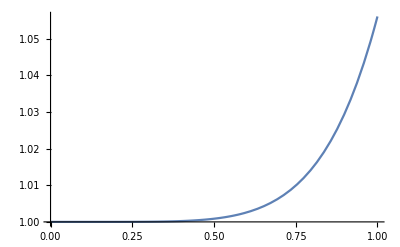

```mathematica
Plot[u1[x],{x,0,1},PlotRange->All]
```

```mathematica
Limit[u1[x],x->0]
```

1

```mathematica
D[u2[x],x]
```

x^2 Cosh[x^3/3]

```mathematica
Limit[D[u2[x],x],x->0]
```

0

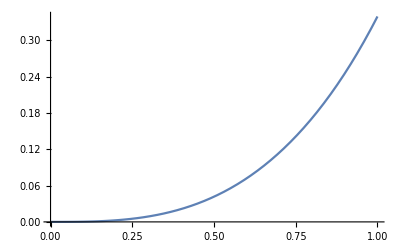

```mathematica
Plot[u2[x],{x,0,1}]
```

```mathematica
u2[0]
```

0

```mathematica
y1[x_]:=u2[x];
```

### BC2 : y'[∞] = 0

```mathematica
Limit[D[u1[x]-u2[x],x],x->∞]
```

0

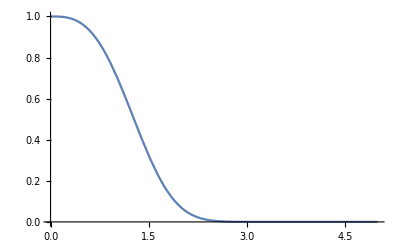

```mathematica
Plot[u1[x]-u2[x],{x,0,5},PlotRange->All]
```

```mathematica
y2[x_]:=u1[x]-u2[x];
```

## Construction of Wronskian

```mathematica
D[y2[x],x]y1[x]-y2[x]D[y1[x],x]//FullSimplify
```

-x^2

```mathematica
W[x_]:=-x^2;
```

## Construction of Inhomogeneous Solution

```mathematica
Off[NIntegrate::inumr]
```

```mathematica
y[x_?NumericQ]:=Quiet[y2[x]NIntegrate[(y1[s] s^4 g[s])/W[s],{s,10^-9,x}]+y1[x]NIntegrate[(y2[s] s^4 g[s])/W[s],{s,x,∞}]];
```

```mathematica
y[2]
```

-0.496716

```mathematica
yTab=Table[{i,0},{i,0.1,6,0.1}];
SetSharedVariable[yTab];
```

```mathematica
Quiet[ParallelDo[yTab[[i,2]]=y[yTab[[i,1]]],{i,1,Length[yTab]}]]
```

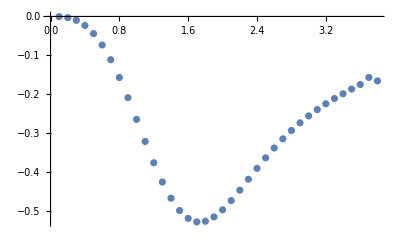

```mathematica
ListPlot[yTab[[;;-23]]]
```

```mathematica
yInter=Interpolation[yTab[[;;-23]]];
```

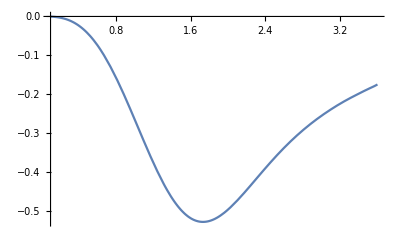

```mathematica
Plot[yInter[x],{x,0.1,3.6}]
```

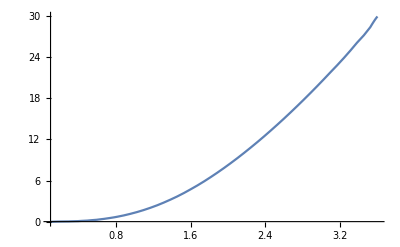

```mathematica
Plot[yInter''[x]-2/x yInter'[x]-x^4 yInter[x],{x,0.1,3.6}]
```

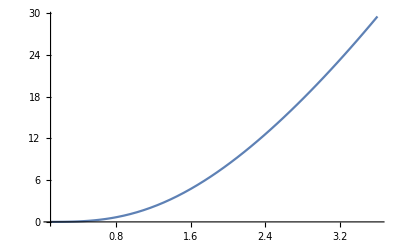

```mathematica
Plot[x^4 g[x],{x,0.1,3.6}]
```

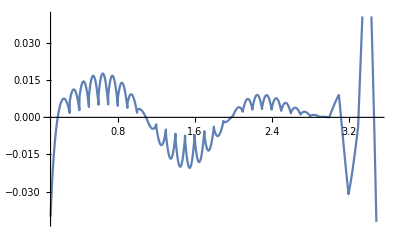

```mathematica
Plot[(yInter''[x]-2/x yInter'[x]-x^4 yInter[x])-(x^4 g[x]),{x,0.1,3.5}]
```